# Essentials of Programming in Mathematica

## Ch.1: Programming With Mathematica

## Exercises

1. Generate a random number between one and one hundred. Then create a vector of twelve random numbers between one and one hundred. Finally create a 4x4 array of such numbers and then compute the determinant of that array.

```mathematica
RandomReal[{1,100},{4,4}]//Det
```

1.81789×10^7

2. Using Table, create a 4x4 Hilbert matrix. The entry aij in row i, column j of the Hilbert matrix is given by . Check your solution against the built-in HilbertMatrix.

```mathematica
Table[1/(i+j-1),{i,1,4},{j,1,4}]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

```mathematica
HilbertMatrix[4]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

```mathematica
%5==%6
```

True

3. Add the two lists, {1, 2, 3, 4, 5} and {2, 4, 6, 8, 10}. Then multiply them element-wise. Finally, multiply the two lists as vectors (dot product).

```mathematica
{1,2,3,4,5}+{2,4,6,8,10}
{1,2,3,4,5}*{2,4,6,8,10}
{1,2,3,4,5}.{2,4,6,8,10}
```

{3,6,9,12,15}

{2,8,18,32,50}

110

4. Generate a list of the first 25 integers in five different ways.

```mathematica
Table[i,{i,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
Range[1,25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
doList={};
Do[AppendTo[doList,i],{i,1,25}];
doList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
forList={};
For[i=1,i≤ 25,i++,AppendTo[forList,i]];
forList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
whileList={};
i=1;
While[i≤ 25,AppendTo[whileList,i];i++];
whileList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

5. Add the integers one through one thousand in as many different ways as you can.

```mathematica
Sum[i,{i,1,1000}]
```

500500

```mathematica
ParallelSum[i,{i,1,1000}]
```

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

500500

```mathematica
Total[Range[1,1000]]
```

500500

```mathematica
Total[Table[i,{i,1,1000}]]
```

500500

```mathematica
i=0;
Do[i=i+j,{j,1,1000}];
i
```

500500

6. A 2×2 matrix can be created using lists such as {{a,b},{c,d}}. Deﬁne a 2×2 numerical matrix and then ﬁnd its inverse, determinant, transpose, and trace.

```mathematica
RandomReal[{0,1},{2,2}]//MatrixForm
```

(0.770901 | 0.772621
0.576254 | 0.497387)

```mathematica
Inverse[%18]//MatrixForm
```

(-8.04975 | 12.5042
9.32613 | -12.4763)

```mathematica
Det[%18]
```

-0.0617891

```mathematica
Transpose[%18]//MatrixForm
```

(0.770901 | 0.576254
0.772621 | 0.497387)

```mathematica
Tr[%18]
```

1.26829

## Ch.2: The Mathematica Language

## Examples

Random walk. Note that Accumulate is not the same as +=; it saves intermediate output.

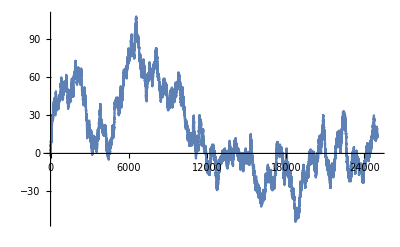

```mathematica
ListLinePlot[Accumulate[RandomChoice[{-1,0,1},{25000}]]]
```

Same but overlaying several random walks.

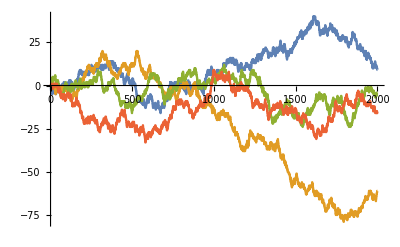

```mathematica
ListStepPlot[Table[Accumulate[RandomChoice[{-1,0,1},{2000}]],{4}]]
```

Random walk as a function

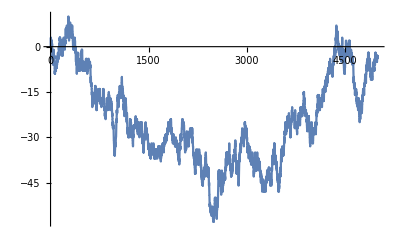

```mathematica
walk[t_]:=Module[{dirs,steps},
dirs={-1,0,1};
steps=RandomChoice[dirs,t];
Accumulate[steps]
];
walk[5000]//ListLinePlot
```

What does Hold do? What does Evaluate do? In first example table is evaluated for each x in Plot. In second example its faster?

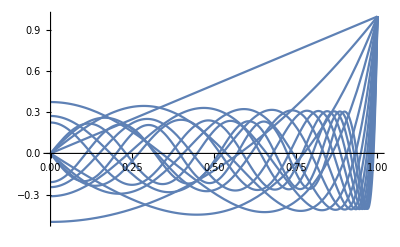
{0.295749,-Graphics-}

```mathematica
Plot[Table[LegendreP[n,x],{n,1,15}],{x,0,1}]//Timing
```

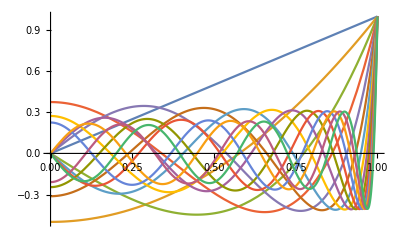
{0.113085,-Graphics-}

```mathematica
Plot[Evaluate@Table[LegendreP[n,x],{n,1,15}],{x,0,1}]//Timing
```

## Exercises

1. Determine if each of the following are atomic expressions. If the expression is not atomic, find its head.

```mathematica
AtomQ[8/5]
```

True

```mathematica
AtomQ[8/5+x]
Head[8/5+x]
```

False

Plus

```mathematica
AtomQ[{{a,b},{c,d}}]
Head[{{a,b},{c,d}}]
```

False

List

```mathematica
AtomQ["8/5+x"]
```

True

2. Give the full (internal) form of the expression a (b + c).

```mathematica
FullForm[a (b+c)]
```

Times[a,Plus[b,c]]

3. What is the traditional representation of Times [a, Power [Plus[b, c], –1]].

```mathematica
Times [a, Power [Plus[b, c], –1]]
```

a (b+c)^–

4. What is the part specification of the symbol b in the expression a x2 + b x + c?

```mathematica
Part[a x2+b x+c,2]
```

b x

5. What will be the result of evaluating each of the following? Use FullForm on the expressions to help you understand their structures.

```mathematica
FullForm[((x^2+y) z/w)[[2,1,2]]]
```

2

```mathematica
FullForm[(a/b)[[2,2]]]
```

-1

6. Use Level to find all the factors in the following expression. Then find all the terms inside the parentheses of the output.

```mathematica
LegendreP[5,x]
```

1/8 (15 x-70 x^3+63 x^5)

```mathematica
Level[%23[[2]],{2}]
```

{15,x,-70,x^3,63,x^5}

7. Explain why the following expression returns an integer instead of displaying the internal representation of the fraction.

8. Modify the code for the one-dimensional random walk in this section to create two-dimensional random walks.

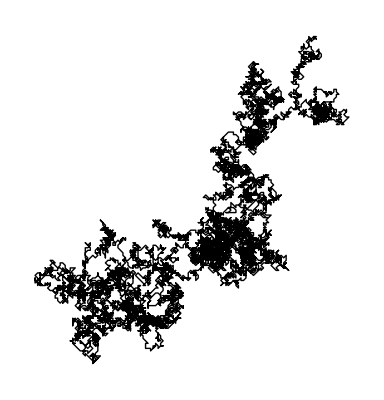

```mathematica
Graphics[Line[Accumulate[RandomChoice[Tuples[{0,1,-1},2],{10000}]]]]
```

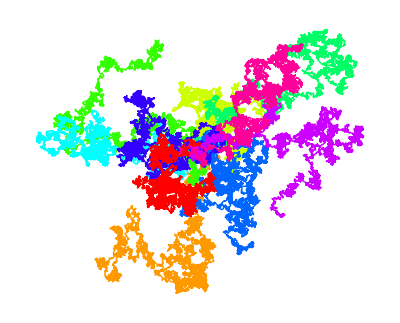

```mathematica
Graphics[Table[{Hue[i/10],Line[Accumulate[RandomChoice[Tuples[{0,1,-1},2],{10000}]]]},{i,1,10}]
]
```

1. Is the expression 2 + π a number? Is it numeric? What is the difference?
It is not a number, it is a numeric.

```mathematica
NumberQ[2+π]
```

False

```mathematica
Head[2+π]
```

Plus

```mathematica
NumericQ[2+π]
```

True

2. Convert the base 10 integer 65 to base 2. Then convert back to base 10.

```mathematica
BaseForm[65,2]
```

```mathematica
Subscript["1000001", "2"]
```

65

```mathematica
2^^1000001
```

65

3. Define a function complexToPolar that converts complex numbers to their polar representations. Then, convert the numbers 3 + 3 i and π/3 to polar form.

```mathematica
complexToPolar[num_]:=Module[{θ,r},
r=Abs[num];
θ=Arg[num];
{r,θ}
];
```

```mathematica
complexToPolar[3+3ⅈ]
```

{3 √2,π/4}

```mathematica
AbsArg[3+3ⅈ]
```

{3 √2,π/4}

4. Use NumberForm to display an approximate number with exactly four precise digits and three digits to the right of the decimal. Then use PaddedForm to display the numbers in the following vector with precisely two digits to the right of the decimal.

```mathematica
NumberForm[N[Pi],{4,3}]
```

3.142

```mathematica
vec=RandomReal[{0,1},8]
```

{0.814211,0.551942,0.960738,0.439451,0.0299773,0.148097,0.153071,0.702443}

```mathematica
PaddedForm[vec,{3,2}]
```

{ 0.81, 0.55, 0.96, 0.44, 0.03, 0.15, 0.15, 0.70}

5. Make a histogram of the frequencies of the first 100 000 digits of π. It is an open problem in number theory as to whether the digits are normal, meaning that each of the digits zero through nine occur with about the same frequency in the decimal expansion of π. See Bailey (2012) for more information on normality and the digits of π.

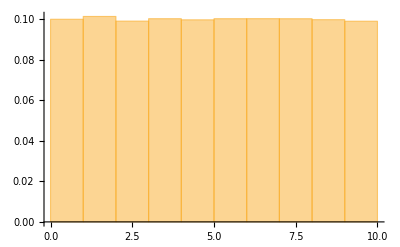

```mathematica
Histogram[RealDigits[N[Pi,100000]],Automatic,"Probability"]
```

6. Convert each of the characters in a string such as “Apple” to their eight-bit binary character code representation.

```mathematica
ToCharacterCode/@Characters["Apple"]//Flatten
```

{65,112,112,108,101}

```mathematica
IntegerDigits[%,2,8]
```

{{0,1,0,0,0,0,0,1},{0,1,1,1,0,0,0,0},{0,1,1,1,0,0,0,0},{0,1,1,0,1,1,0,0},{0,1,1,0,0,1,0,1}}

7. Extract the first 5000 digits in the decimal expansion of 1/17 or any other rational number. Then play them using ListPlay which emits sound whose amplitude is given by the sequence of digits. Compare with the first 5000 digits of π.

```mathematica
N[1/17,10]
```

0.05882352941

8. Graphs consist of a set of vertices and edges connecting some subset of those vertices. They are implemented in Mathematica with Graph, which takes two arguments: a list of vertices and a list of edges. Create a random graph on n vertices by choosing m edges from the  possible edges. Such random graphs are commonly specified as G(n, m) and are essentially the model upon which the built-in RandomGraph is based.

```mathematica
makeEdges[n_,m_]:=Subsets[Range[1,n],{2}]//RandomSample[#,m]&//EdgeList;
```

```mathematica
makeEdges[20,5]
```

{2<->16,11<->20,10<->12,6<->9,9<->19}

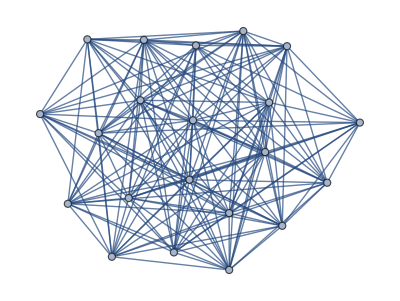

```mathematica
Graph[makeEdges[21,167]]
```

9. RandomReal by default outputs numbers uniformly distributed on the interval [0, 1]. Bias the random number generator towards the lower end of this interval giving a histogram similar to those below.

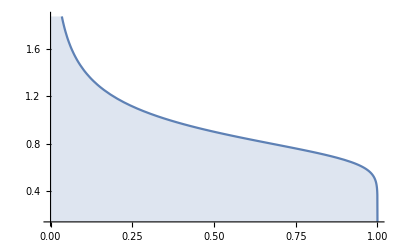

```mathematica
Plot[PDF[BetaDistribution[.75,1.1],x],{x,0,1},Filling->Axis]
```

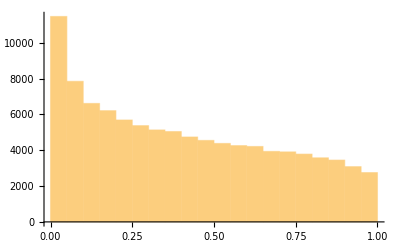

```mathematica
RandomVariate[BetaDistribution[.75,1.1],100000]//Histogram
```

10. Information theory, as conceived by Claude Shannon in the 1940s and 1950s, was originally interested in maximizing the amount of data that can be stored and retrieved over some channel such as a telephone line. Shannon devised a measure, now called the entropy, that gives the theoretical maxima for such a signal. Entropy can be thought of as the average uncertainty of a single random variable and is computed by the following, where p(x) is the probability of event x over a domain X:
H(X) = –∑x∈X p(x) log2 p(x)
Generate a plot of the entropy (built into Mathematica as Entropy) as a function of success probability.

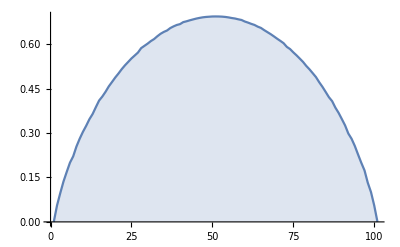

```mathematica
Entropy/@Table[RandomVariate[BernoulliDistribution[p],100000],{p,0,1,0.01}]//ListLinePlot[#,Filling->Axis]&
```

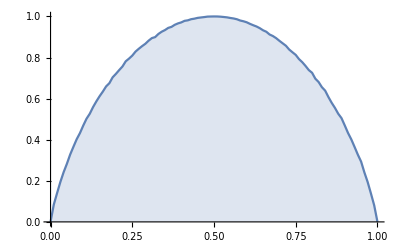

```mathematica
Table[{p,Entropy[2,RandomVariate[BernoulliDistribution[p],100000]]},{p,0,1,0.01}]//ListLinePlot[#,Filling->Axis]&
```

1. Create a function reciprocal[] that returns the reciprocal of the fraction a/b. Check your answer with numeric and symbolic fractions as well as with fractions containing zero in the numerator.

```mathematica
reciprocal[Rational[a_,b_]]:=Rational[b,a];
```

```mathematica
reciprocal[5/2]
```

2/5

2. Using Total, create a function to sum the first n positive integers.

```mathematica
sumInt[n_]:=Total[Range[1,n]];
```

```mathematica
sumInt[5]
```

15

3. Create a function to compute the sum of the digits of any integer. Write an additional rule to give the sum of the base-b digits of an integer. Then use your function to compute the Hamming weight of any integer: the Hamming weight of an integer is given by the number of ones in the binary representation of that number. It has wide use in computer science (modular exponentiation and hash tables), cryptography, and coding theory (Knuth 2011).

```mathematica
hammingWeight[int_]:=Module[{sumDig,sumB,hamW},
sumDig=IntegerDigits[int]//Total;
sumB=IntegerDigits[int,2]//Total;
hamW=IntegerDigits[int,2]//Count[#,1]&;
{sumDig,sumB,hamW}
];
hammingWeight[24355]
```

{19,9,9}

4. Write a function sumsOfCubes [n] that takes a positive integer argument n and computes the sums of cubes of the digits of n (Hayes 1992).

```mathematica
sumsOfCubes[n_]:=Total[IntegerDigits[n]^3];
```

```mathematica
sumsOfCubes[124]
```

73

8. Create a piecewise-defined function g(x) based on the following; plot the function from –2 to 0.

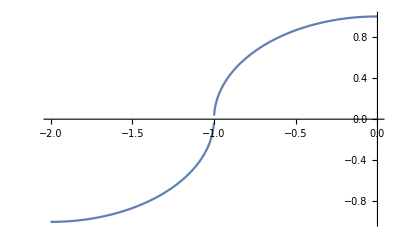

```mathematica
g[x_]:=Piecewise[{
{-Sqrt[1-(x+2)^2],-2≤x≤-1},
{Sqrt[1-x^2],x<0}
}];
Plot[g[x],{x,-2,0}]
```

9. The built-in function RotateRight rotates the elements in a list one place to the right with the last element swinging around to the front. Create a function IntegerRotateRight [n] that takes an integer n and returns an integer with the original digits rotated one place to the right.

```mathematica
RotateRight[{a,b,c,d,e}]
```

{e,a,b,c,d}

```mathematica
IntegerRotateRight[n_]:=Prepend[IntegerDigits[n]//Most,IntegerDigits[n]//Last]//Flatten;
```

```mathematica
IntegerRotateRight[142857]
```

714285

```mathematica
Divisors[%]//Position[#,142857]&
```

{{62}}

10. The Champernowne constant is a famous number that is created by concatenating successive integers and interpreting them as decimal digits. Concatenation can used to create integers also. Create a function to generate the nth Smarandache-Wellin number, formed by concatenating the digits of successive primes. The first such number is 2, then 23, then 235, followed by 2357, 235711, and so on. Numerous open questions exist about these numbers: for example it is not known if an infinite number of them are prime; see Crandall and Pomerance (2005) and Sloane (A019518).

```mathematica
N[ChampernowneNumber[10],31]
```

0.123456789101112131415161718192

```mathematica
smNumber[n_]:=Table[Prime[i],{i,1,n}]//IntegerDigits//Flatten//FromDigits;
smNumber[5]
```

235711

```mathematica
Table[smNumber[i],{i,1,10}]
```

{2,23,235,2357,235711,23571113,2357111317,235711131719,23571113171923,2357111317192329}

1. Create a predicate function that returns a value of True if its argument is between –1 and 1.

```mathematica
predF[x_]:=-1<x<1;
Table[predF[i],{i,-2,2,0.1}]
```

{False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False}

2. Define a predicate function StringCharacterQ [str] that returns true if its argument str is a single string character, and returns false otherwise.

```mathematica
StringCharacterQ[str_]:=StringQ[str]&&StringLength[str]==1;
StringCharacterQ["i"]
```

True

3. Write a predicate function NaturalQ [n] that returns a value of True if n is a natural number and False otherwise, that is, NaturalQ [n] is True if n is among 0, 1, 2, 3, ….

```mathematica
NaturalQ[n_]:=IntegerQ[n]&&n>0;
NaturalQ/@{5,2.3,3,-1}
```

{True,False,True,False}

4. Create a predicate function, SquareNumberQ [n] that returns True if n is a square number, such as 1, 4, 9, 16,….

```mathematica
SquareNumberQ[n_]:=Mod[n,Sqrt[n]]==0;
SquareNumberQ/@{1,4,9,3,3.23}
```

{True,True,True,False,False}

```mathematica
Select[Range[100],SquareNumberQ]
```

{1,4,9,16,25,36,49,64,81,100}

5. Create a predicate function TriangularNumberQ [t] that returns True whenever its argument t is a triangular number.

```mathematica
TriangularNumberQ[t_]:=OddQ[Sqrt[8t+1]&&SquareNumberQ[8t+1]];
TriangularNumberQ/@{6,55,56}
```

{True,True,False}

6. Based on the solution to the two previous exercises, create a predicate function SquareTriangularNumberQ [n] that returns a value of True if n is both a square number and a triangular number. Then use this predicate to find all square triangular numbers less than one million.

```mathematica
SquareTriangularNumberQ[n_]:=SquareNumberQ[n]&&TriangularNumberQ[n];
Select[Range[1000000],SquareTriangularNumberQ]
```

{1,36,1225,41616}

7. Create a predicate function RealPositiveQ [x] that returns True if x is a positive real number (“real” in the mathematical sense, i.e., x ∈ ). Add a second rule that accepts vectors as arguments and returns True if every element of the vector argument is a positive real number.

```mathematica
RealPositiveQ[x_]:=Element[x,Reals]&&Positive[x];
Select[{-4,23,3+4I,π},RealPositiveQ]
```

{23,π}

```mathematica
RealPositiveQ[vec_?VectorQ]:=AllTrue[vec,RealPositiveQ];
```

8. The built-in function CoprimeQ [a, b] returns True if a and b are relatively prime (share no common factors other than 1) and returns False otherwise. Use ArrayPlot to visualize pairs of relatively prime numbers from 1 to 100. Use Boole to convert the table of True/False values returned by CoPrimeQ to zeros and ones.

```mathematica
Table[CoprimeQ[i,j],{i,100},{j,100}]//Boole//ArrayPlot
```

-Graphics-

9. Define a function DenseGraphQ [gr] that returns a value of True if gr is dense in the above sense and returns a value of False otherwise. CompleteGraph [n] should return True for any n.

```mathematica
DenseGraphQ[gr_]:=Module[{E,V,D},
E=EdgeCount[gr];
V=VertexCount[gr];
D=E/(V*(V-1));
D≥ 0.5
];
CompleteGraph[5]//DenseGraphQ
RandomGraph[{10,20}]//DenseGraphQ
```

True

False

1. Use one of the Hold attributes to give g the property that its argument is not evaluated first.

```mathematica
g[x_+y_]:=x^2+y^2;
SetAttributes[g,HoldAll];
```

```mathematica
(*This is the behavior we want*)
g[2+3]
```

13

```mathematica
(*this is bad*)
ClearAll[g];
g[x_+y_]:=x^2+y^2;
g[2+3]
```

g[5]

3. Define a function that takes each number, x, in a vector of numbers and returns x if it is within a certain interval, say –0.5 < x < 0.5, and returns  otherwise. Then make your function listable so that it can operate on vectors (lists) directly.

```mathematica
intervalCheck[x_]:=If[-0.5<x<0.5,x,Sqrt[x]];
SetAttributes[intervalCheck,Listable];
Table[intervalCheck[i],{i,-1,1,0.1}]
```

{0.+1. ⅈ,0.+0.948683 ⅈ,0.+0.894427 ⅈ,0.+0.83666 ⅈ,0.+0.774597 ⅈ,0.+0.707107 ⅈ,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.707107,0.774597,0.83666,0.894427,0.948683,1.}

## Ch.3: Lists and Associations

## Examples

Use Table with 2 iterators

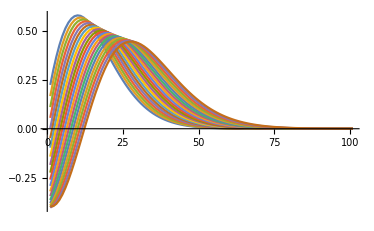

```mathematica
Table[BesselJ[i,j],{j,2,4,0.1},{i,0,10,0.1}]//ListLinePlot
```

Order of the iterators is important. iterate over the inner first and the outer second. 
for(i in 1:4){
    for(j in 1:i){
        c(i,j)
    }
}

```mathematica
Table[{i,j},{i,1,4},{j,1,i}]
```

{{{1,1}},{{2,1},{2,2}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3},{4,4}}}

Array is like “outer” in R.

```mathematica
Array[Times,{4,4}]//MatrixForm
```

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16)

Quickly view listception

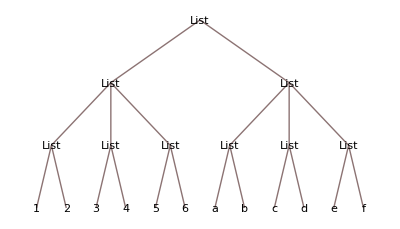

```mathematica
TreeForm[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

Replacement of lists in a matrix example, replace outer parts by 0s

```mathematica
matRep=ConstantArray[1,{5,5}];
matRep//MatrixForm
matRep[[{1,-1},All]]=0;(*set the first and last rows equal to 0 over all columns*)
matRep//MatrixForm
matRep[[All,{1,-1}]]=0;(*set the first and last columns equal to 0 over all rows*)
matRep//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)

(0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0)

## Exercises

1. Create a list of the multiples of 5 less than or equal to 100

```mathematica
Table[5j,{j,1,100/5}]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

```mathematica
Range[5,100,5]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

2. Create a list of the reciprocals of the powers of 2 as the powers go from zero to sixteen.

```mathematica
Table[1/2^i,{i,0,16}]
```

{1,1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024,1/2048,1/4096,1/8192,1/16384,1/32768,1/65536}

3. Generate the list {{0}, {0, 2}, {0, 2, 4}, {0, 2, 4, 6}, {0, 2, 4, 6, 8}} in two different ways using the Table function.

```mathematica
Table[j,{i,0,8,2},{j,0,i,2}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

```mathematica
Table[f[i],{i,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[f[i,j],{i,1,3},{j,1,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

5. Using Table, create an nxn matrix consisting of the positive integers one through n2 arranged such that the first row is the list, {1, 2, 3, …, n}, the second row is the list {1 + n, 2 + n, 3 + n, …, 2 n}, and in general the kth row is the list {1 + (k – 1) n, 2 + (k – 1) n, 3 + (k – 1) n, …, n2}.

```mathematica
Table[1+i+j,{i,0,4^2-1,4},{j,0,4-1}]//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16)

6. Using Table, create a symmetric matrix of the binomial coefficients for any n similar to that in the following table.

```mathematica
Table[Binomial[i+j,i],{i,0,4},{j,0,4}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 5
1 | 3 | 6 | 10 | 15
1 | 4 | 10 | 20 | 35
1 | 5 | 15 | 35 | 70)

8. Given an mm square lattice like the grid graph below, color all vertices on the bottom red, on the top white. Your solution should be as general as possible, so that changing the size of the lattice (changing the value of m) will still work to color the lattice.

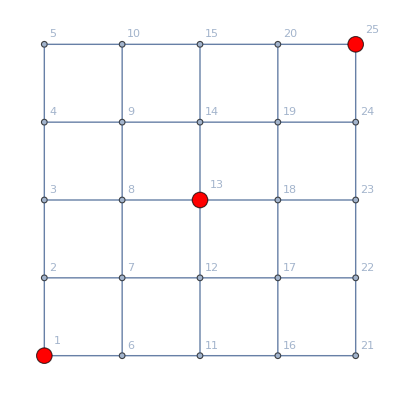

```mathematica
GridGraph[{5,5},VertexLabels->"Name"]//HighlightGraph[#,Style[{1,13,25},Red],VertexSize->Medium]&
```

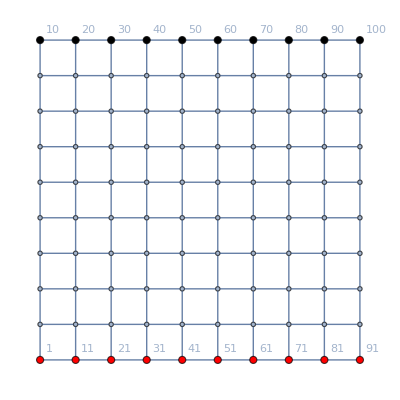

```mathematica
colorGraph[m_]:=GridGraph[{m,m}]//HighlightGraph[#,{Style[Range[1,m^2,m],Red],Style[Range[m,m^2,m],Black]},VertexSize->Medium,VertexLabels->"Name"]&;
colorGraph[10]
```

9. Construct an integer lattice graphic like that below.

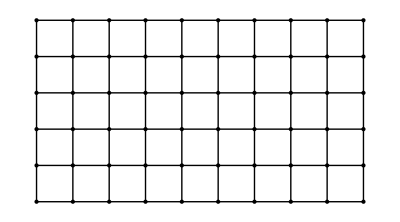

```mathematica
Lattice[x_,y_]:=Module[{coords},
coords=CoordinateBoundsArray[{{1,x},{1,y}}];
Graphics[{
Line[coords],Line[Transpose[coords]],PointSize[Medium],Point[Flatten[coords,1]]
}]
];
Lattice[10,6]
```

1. What is the length of the following list? What are its dimensions? What is the position of g?

```mathematica
Dimensions[{{a, b}, {c, d}, {e, f}, {g, h}}]
Length[{{a, b}, {c, d}, {e, f}, {g, h}}]
Position[{{a, b}, {c, d}, {e, f}, {g, h}},g]
```

{4,2}

4

{{4,1}}

2. The following input generates a list of 10 000 zeros and ones weighted heavily towards the ones. Determine if there are any zeros in this list and if there are, find how many.

```mathematica
lis=RandomChoice[{0.0001,0.9999}-> {0,1},10000];
```

```mathematica
AnyTrue[lis,#==0&]
```

True

```mathematica
Count[lis,0]
```

1

3. Given a list of integers such as the following, count the number of zeros. Find a way to count all those elements of the list which are not ones.

```mathematica
ints=RandomInteger[{-5,5},30];
```

```mathematica
Count[ints,Except[0]]
```

25

```mathematica
Count[ints,0]
```

5

4. Given the list {{{1, a}, {2, b}, {3, c}}, {{4, d}, {5, e}, {6, f}}}, determine its dimensions. Use the Dimensions function to check your answer.

```mathematica
Dimensions[{{{1,a},{2,b},{3,c}},{{4,d},{5,e},{6,f}}}]
```

{2,3,2}

5. Find the positions of the nines in the following list.

```mathematica
Position[{{2,1,10},{9,5,7},{2,10,4},{10,1,9},{6,1,6}},9]
```

{{2,1},{4,3}}

6. Determine if there are any prime numbers in the interval [4 302 407 360, 4 302 407 713]. Once you have a list of the integers that you want to test for primality, use Position (see Section 4.1) and Extract to return the explicit primes

```mathematica
Position[Range[4302407360,4302407713],p_?PrimeQ]//Extract[Range[4302407360,4302407713],#]&
```

{4302407713}

1. Given a list of data points such as the following,
          {{x1, y1}, {x2, y2}, {x3, y3}, {x4, y4}, {x5, y5}},
separate the x and y components to get:
          {{x1, x2, x3, x4, x5}, {y1, y2, y3, y4, y5}}

```mathematica
dat={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}};
Join[{dat[[All,1]]},{dat[[All,2]]}]
```

{{x1,x2,x3,x4,x5},{y1,y2,y3,y4,y5}}

2. Use the Part function to extract the elements of a list that are in the even-indexed positions. So in the list below, the even-indexed elements are {3, 8, 3, 4, 2, 13}. Then extract all those elements in the odd-indexed positions.

```mathematica
lis={5,3,3,8,17,3,3,4,20,2,11,13};
Take[lis,{2,Length[lis],2}]
Take[lis,{1,Length[lis]-1,2}]
```

{3,8,3,4,2,13}

{5,3,17,3,20,11}

3. Given the following list of integers, find the five largest numbers in the list. Then find the five smallest numbers in the list.

```mathematica
nums=RandomInteger[{-100,100},{25}];
Sort[nums][[Range[1,5]]] (*five smallest*)
```

{-97,-93,-86,-85,-84}

```mathematica
Reverse[Sort[nums]][[Range[1,5]]] (*five largest*)
```

{100,97,92,86,73}

4. Use Table to create the following matrix. Once created, use Table again to add all the elements on and above the diagonal.

```mathematica
matrix=Table[i*j,{i,1,4},{j,1,4}];
matrix//MatrixForm
```

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16)

```mathematica
Table[matrix[[i,j]],{i,1,4},{j,i,4}]//Flatten[#,1]&//Total
```

65

5. Rearrange the list of numbers one through ten so that any adjacent numbers (for example, 1 and 2, 2 and 3, and so on) are not adjacent in the output.

```mathematica
nums=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
oddNums=Take[nums,{1,10,2}]
```

{1,3,5,7,9}

```mathematica
evenNums=Complement[nums,oddNums]
```

{2,4,6,8,10}

```mathematica
Riffle[RotateLeft[evenNums],oddNums]
```

{4,1,6,3,8,5,10,7,2,9}

```mathematica
Partition[nums,5]//Riffle[#[[1]],#[[2]]]& (*so much more elegant*)
```

{1,6,2,7,3,8,4,9,5,10}

6. Create a list of all prime numbers less than 100. Repeat for a list of primes less than 1000. Consider using the functions Prime and PrimePi

```mathematica
PrimePi[100]//Prime[Range[1,#]]&
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
PrimePi[1000]//Prime[Range[1,#]]&
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997}

7. Make a histogram of the frequencies of the leading digit in the first 10 000 Fibonacci numbers. The resulting distribution is an instance of Benford’s Law, which concerns the frequency of the leading digits in many kinds of data. The phenomenon, whereby a 1 occurs about 30% of the time, a 2 occurs about 17.6% of the time, and so on, has been shown to occur in well-known numerical sequences, population counts, death rates, Fibonacci numbers, and many more, and has even been used to detect corporate and tax fraud.

```mathematica
fibonacciSeq[n_]:=Module[{out={1,1}},
Table[AppendTo[out,out[[i-2]]+out[[i-1]]],{i,3,n}];
out
];
```

```mathematica
firstTenThousand=fibonacciSeq[10000];
```

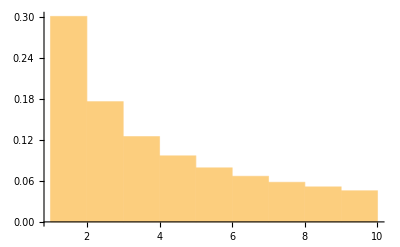

```mathematica
First[IntegerDigits[#]]&/@firstTenThousand//Histogram[#,Automatic,"Probability"]&
```

8. Take the partitioned list of integers from the solution to Exercise 5 in Section 3.1 and use Grid to display the partitioned list in a grid similar to the one below.